## Lesson 24: Discontinuous forcing functions

## Overview

Now that you understand how to construct and transform step functions, you can solve differential equations with discontinuous nonhomogeneous terms.

This allows solving a much more extensive class of spring-mass problems and flow of current problems where the external force is not a continuous function, such as a switch:

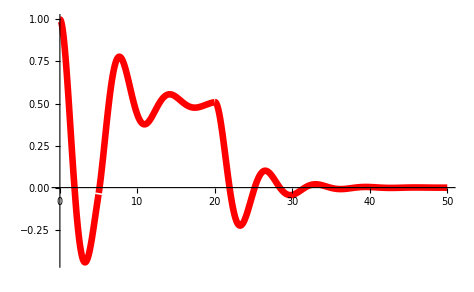

```mathematica
sln=DSolveValue[{2y''[t]+y'[t]+2y[t]==UnitStep[t-5]-UnitStep[t-20],y[0]==1,y'[0]==0},y[t],t];
Plot[sln,{t,0,50},]
```

## Example 1

Find the solution of the differential equation:

2 y''(t)+y'(t)+2 y(t)=U(t-1)

y(0)=1

y'(0)=0

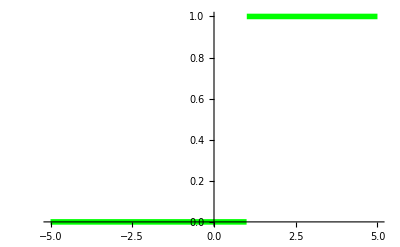

```mathematica
Plot[UnitStep[t-1],{t,-5,5},]
```

Through the use of the LaplaceTransform, this becomes quite easily solvable:

```mathematica
eqn=2y''[t]+y'[t]+2y[t]==UnitStep[t-1]
```

2 y[t]+y'[t]+2 y''[t]==UnitStep[-1+t]

## Example 1

First, apply LaplaceTransform and replace y(0) and y'(0) with their respective values:

```mathematica
lt=(LaplaceTransform[eqn,t,s]/.{y[0]->1,y'[0]->0})
```

-1+2 LaplaceTransform[y[t],t,s]+s LaplaceTransform[y[t],t,s]+2 (-s+s^2 LaplaceTransform[y[t],t,s])==ⅇ^-s/s

Solve for L{y(t)}:

```mathematica
Solve[lt,LaplaceTransform[y[t],t,s]]
```

{{LaplaceTransform[y[t],t,s]→(ⅇ^-s (1+ⅇ^s s+2 ⅇ^s s^2))/(s (2+s+2 s^2))}}

Now you can apply InverseLaplaceTransform to recover the solution to the differential equation:

```mathematica
sln=InverseLaplaceTransform[(ⅇ^-s (1+ⅇ^s s+2 ⅇ^s s^2))/(s (2+s+2 s^2)),s,t]
```

HeavisideTheta[-1+t] (1/2-(ⅇ^((1-t)/4) (√15 Cos[1/4 √15 (-1+t)]+Sin[1/4 √15 (-1+t)]))/(2 √15))+(ⅇ^(-t/4) (√15 Cos[(√15 t)/4]-Sin[(√15 t)/4]))/(√15)+(2 ⅇ^(-t/4) Sin[(√15 t)/4])/(√15)

## Example 1

You can directly observe the effect of the nonhomogeneous term on the path the solution takes:

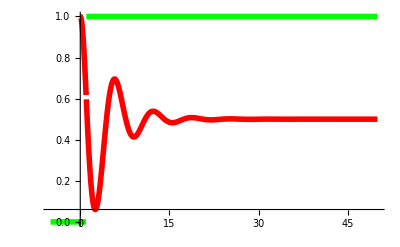

```mathematica
Show[Plot[sln,{t,0,50},],Plot[UnitStep[t-1],{t,-5,50},]]
```

You can use DSolveValue to verify this result:

```mathematica
sln2=DSolveValue[{eqn,y[0]==1,y'[0]==0},y[t],t];
```

Plot the solution over time:

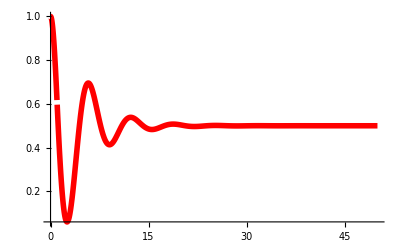

```mathematica
Plot[sln2,{t,0,50},]
```

## Example 2

Find the solution of the differential equation:

y''(t)+4 y(t)=(U(t-5)(t-5)-U(t-15)(t-15))/10

y(0)=1

y'(0)=0

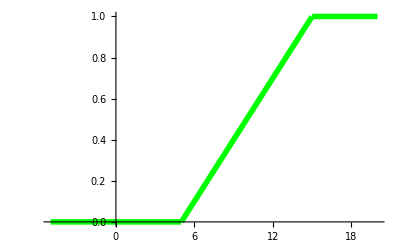

```mathematica
Plot[(UnitStep[t-5]*(t-5)-UnitStep[t-15]*(t-15))/10,{t,-5,20},]
```

Through the use of  LaplaceTransform, this becomes quite easily solvable.

First, define the equation:

```mathematica
eqn=y''[t]+4y[t]==(UnitStep[t-5](t-5)-UnitStep[t-15](t-15))/10;
```

## Example 2

Apply LaplaceTransform:

```mathematica
lt=LaplaceTransform[eqn,t,s]
```

4 LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]-s y[0]-y'[0]==1/10 (ⅇ^(-5 s) (1/s^2+5/s)-ⅇ^(-15 s) (1/s^2+15/s)+(15 ⅇ^(-15 s))/s-(5 ⅇ^(-5 s))/s)

Replace y(0) and y'(0) with their respective values:

```mathematica
lt2=lt/.{y[0]->1,y'[0]->0}
```

-s+4 LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]==1/10 (ⅇ^(-5 s) (1/s^2+5/s)-ⅇ^(-15 s) (1/s^2+15/s)+(15 ⅇ^(-15 s))/s-(5 ⅇ^(-5 s))/s)

Solve for L{y(t)}:

```mathematica
Solve[lt2,LaplaceTransform[y[t],t,s]]
```

{{LaplaceTransform[y[t],t,s]→(ⅇ^(-15 s) (-1+ⅇ^(10 s)+10 ⅇ^(15 s) s^3))/(10 s^2 (4+s^2))}}

Now you can apply the function InverseLaplaceTransform to recover the solution to the differential equation:

```mathematica
sln=InverseLaplaceTransform[(ⅇ^(-15 s) (-1+ⅇ^(10 s)+10 ⅇ^(15 s) s^3))/(10 s^2 (4+s^2)),s,t]
```

1/10 (10 Cos[2 t]+1/4 HeavisideTheta[-5+t] (-5+t+Cos[5-t] Sin[5-t])-1/4 HeavisideTheta[-15+t] (-15+t+Cos[15-t] Sin[15-t]))

## Example 2

Observe the effect that the ramp function has on the solution as its path is gradually displaced in the positive direction:

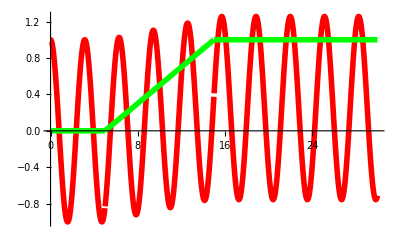

```mathematica
Show[Plot[sln,{t,0,30},],Plot[(UnitStep[t-5](t-5)-UnitStep[t-15](t-15))/10,{t,0,30},]]
```

You can use DSolveValue to verify this result:

```mathematica
sln2=DSolveValue[{eqn,y[0]==1,y'[0]==0},y[t],t];
```

Plot the solution over time:

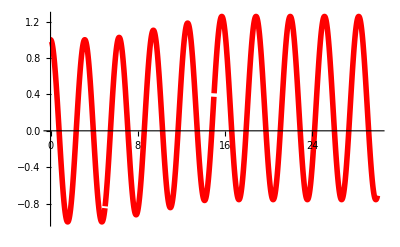

```mathematica
Plot[sln2,{t,0,30},PlotStyle->{Thickness[0.01],Red}]
```

## Example 3

Find the solution of the differential equation:

2 y''(t)+y'(t)+2 y(t)=U(t-5)-U(t-20)

y(0)=1

y'(0)=0

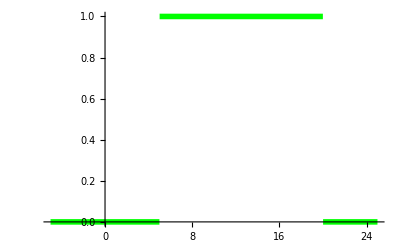

```mathematica
Plot[UnitStep[t-5]-UnitStep[t-20],{t,-5,25},]
```

Define the equation:

```mathematica
eqn=2y''[t]+y'[t]+2y[t]==UnitStep[t-5]-UnitStep[t-20];
```

## Example 3

First, you can apply LaplaceTransform through the following commands:

```mathematica
lt=LaplaceTransform[eqn,t,s]
```

2 LaplaceTransform[y[t],t,s]+s LaplaceTransform[y[t],t,s]-y[0]+2 (s^2 LaplaceTransform[y[t],t,s]-s y[0]-y'[0])==-ⅇ^(-20 s)/s+ⅇ^(-5 s)/s

Next, replace y(0) and y'(0) with their respective values:

```mathematica
lt2=lt/.{y[0]->1,y'[0]->0}
```

-1+2 LaplaceTransform[y[t],t,s]+s LaplaceTransform[y[t],t,s]+2 (-s+s^2 LaplaceTransform[y[t],t,s])==-ⅇ^(-20 s)/s+ⅇ^(-5 s)/s

As before, solve for L{y(t)}:

```mathematica
Solve[lt2,LaplaceTransform[y[t],t,s]]
```

{{LaplaceTransform[y[t],t,s]→(ⅇ^(-20 s) (-1+ⅇ^(15 s)+ⅇ^(20 s) s+2 ⅇ^(20 s) s^2))/(s (2+s+2 s^2))}}

Now apply the function InverseLaplaceTransform to recover the solution to the differential equation:

```mathematica
sln=InverseLaplaceTransform[(ⅇ^(-20 s) (-1+ⅇ^(15 s)+ⅇ^(20 s) s+2 ⅇ^(20 s) s^2))/(s (2+s+2 s^2)),s,t]
```

-HeavisideTheta[-20+t] (1/2-(ⅇ^((20-t)/4) (√15 Cos[1/4 √15 (-20+t)]+Sin[1/4 √15 (-20+t)]))/(2 √15))+HeavisideTheta[-5+t] (1/2-(ⅇ^((5-t)/4) (√15 Cos[1/4 √15 (-5+t)]+Sin[1/4 √15 (-5+t)]))/(2 √15))+(ⅇ^(-t/4) (√15 Cos[(√15 t)/4]-Sin[(√15 t)/4]))/(√15)+(2 ⅇ^(-t/4) Sin[(√15 t)/4])/(√15)

## Example 3

The solution takes a seemingly impossible path as a result of the discontinuous nonhomogeneous terms:

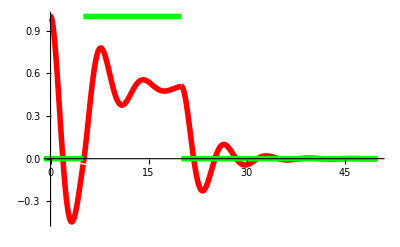

```mathematica
Show[Plot[sln,{t,0,50},],Plot[UnitStep[t-5]-UnitStep[t-20],{t,-5,50},]]
```

You can use DSolveValue to verify this result:

```mathematica
sln2=DSolveValue[{eqn,y[0]==1,y'[0]==0},y[t],t];
```

Plot the solution over time:

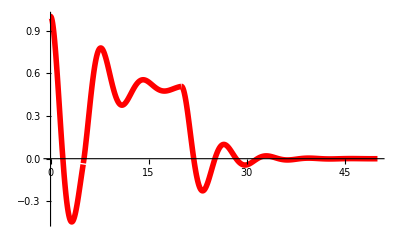

```mathematica
Plot[sln2,{t,0,50},]
```

## Example 3

A comparison to the homogeneous and nonhomogeneous solutions reveals the impact the forcing term has on the solution:

```mathematica
Plot[sln2,{t,0,50},]
```

-Graphics-

Define the homogeneous equation:

```mathematica
eqn2=2y''[t]+y'[t]+2y[t]==0;
```

Solve the initial value problem:

```mathematica
sln3=DSolveValue[{eqn2,y[0]==1,y'[0]==0},y[t],t]
```

1/15 ⅇ^(-t/4) (15 Cos[(√15 t)/4]+√15 Sin[(√15 t)/4])

Observe the solution to the homogenous equation:

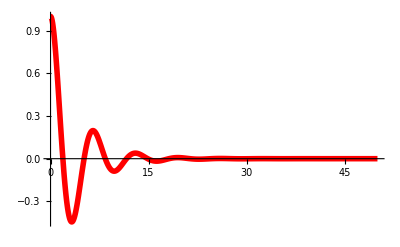

```mathematica
Plot[sln3,{t,0,50},]
```

## Summary

You used your new knowledge of step functions to solve a class of functions whose nonhomogeneous term is discontinuous.

By applying LaplaceTransform to the equation, the solution method only requires a few more additional steps.

With this, you can describe a wider variety of systems with differential equations.